# Audio from noisy undersampled oscillograph

From Nov 1923 Popular Science article on telephony, The Great American Voice by R. W. King, editor Bell System Technical Journal.
The article includes a reproduction of an oscillograph trace, originally 3 feet long, rendered as two strips each as wide as a page.

```mathematica
names = Array["c:/Users/mg/Desktop/maca/america-c"<>ToString[#]<>".PNG"&,2];
a1=Import/@names;
a1
```

{-Graphics-,-Graphics-}

```mathematica
a1g=Thread[ColorConvert[a1,"Grayscale"]];
d=Map[ImageData[#,Interleaving->False]&,a1g];
cols =Map[Transpose[#]&,d];
Map[Image[#]&,cols]
sig = Join@@cols;
Length[sig]
Tally[Length/@sig]
```

ColorConvert::imgcstype: "Grayscale" is an invalid color space specification.

{-Graphics-,-Graphics-}

2763

{{160,1382},{163,1381}}

```mathematica
chunk =Take[sig,{1,100},{15,120}];

Manipulate[
im = Image[chunk];
im =Sharpen[im,s];
ImageResize[im,1200],
{s,0,10,1}
]
```

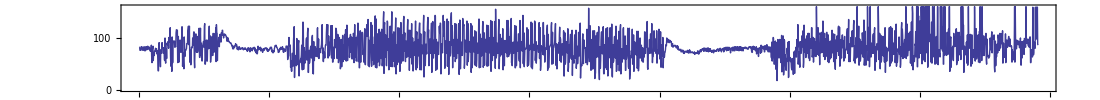

-Graphics-

```mathematica
whereMax[x_]:=Position[x,Max[x]][[1]][[1]];
sigg[cols_]:=Array[whereMax[MovingAverage[cols[[#]],2]] &,Length[cols]];
ListPlot[sigg[sig],ImageSize->{1100,100},Frame->True,AspectRatio->Automatic,Joined->True]
ListPlay[sigg[sig],SampleRate->2800]
```

Exploring the data

```mathematica
c=sig[[1]]
```

{0.0941176,0.121569,0.156863,0.176471,0.176471,0.172549,0.176471,0.184314,0.196078,0.152941,0.137255,0.145098,0.152941,0.164706,0.14902,0.109804,0.101961,0.117647,0.117647,0.121569,0.129412,0.105882,0.0862745,0.0980392,0.133333,0.133333,0.137255,0.145098,0.14902,0.152941,0.156863,0.156863,0.168627,0.192157,0.207843,0.2,0.188235,0.184314,0.184314,0.184314,0.207843,0.2,0.176471,0.160784,0.172549,0.211765,0.239216,0.254902,0.168627,0.172549,0.207843,0.219608,0.2,0.192157,0.203922,0.188235,0.231373,0.231373,0.207843,0.196078,0.215686,0.219608,0.203922,0.188235,0.196078,0.2,0.219608,0.239216,0.239216,0.227451,0.235294,0.254902,0.262745,0.266667,0.423529,0.67451,0.835294,0.858824,0.807843,0.737255,0.792157,0.847059,0.890196,0.905882,0.839216,0.65098,0.443137,0.356863,0.360784,0.364706,0.388235,0.388235,0.368627,0.360784,0.345098,0.305882,0.333333,0.266667,0.239216,0.247059,0.247059,0.227451,0.196078,0.14902,0.160784,0.2,0.219608,0.180392,0.176471,0.247059,0.258824,0.180392,0.211765,0.168627,0.156863,0.180392,0.192157,0.156863,0.117647,0.105882,0.117647,0.0901961,0.0941176,0.164706,0.2,0.14902,0.12549,0.172549,0.207843,0.176471,0.145098,0.12549,0.105882,0.0980392,0.121569,0.156863,0.172549,0.172549,0.176471,0.196078,0.223529,0.223529,0.25098,0.313725,0.219608,0.156863,0.145098,0.188235,0.235294,0.25098,0.223529,0.172549,0.176471,0.176471,0.14902,0.121569,0.145098,0.211765,0.235294,0.215686}

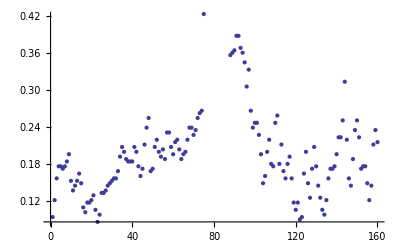

```mathematica
ListPlot[c]
```

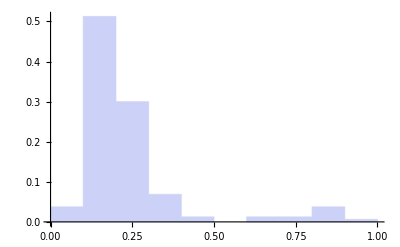

```mathematica
Histogram[c,"Scott","Probability"]
```

```mathematica
Manipulate[
Show[
ListPlot[{MovingAverage[sig[[in]],5]},PlotRange->1.0],
ListPlot[{Position[sig[[in]],Max[sig[[in]]]][[1]][[1]],1},PlotRange->{Length[sig[[in]]],1.0}]
],
{in,1,Length[sig],1}]
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

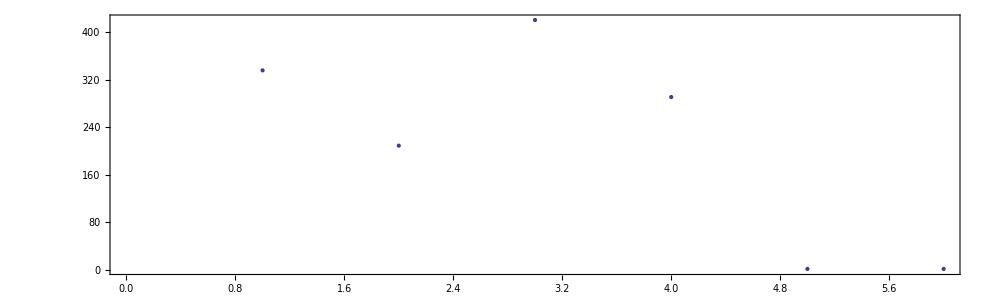

```mathematica
whereMax[x_]:=Position[x,Max[x]][[1]][[1]];
sigg[cols_]:=Table[whereMax[MovingAverage[cols[[in]],1]],{in,1,Length[cols]}];
ListPlot[sigg[cols],ImageSize->{1000,300},Frame->True,AspectRatio->Automatic]
```

```mathematica
ListPlay[sig,SampleRate->1300]
```

-Graphics-

# Does excess gain + hysteresis cause hunting?

The variac rotor doesn’t turn immediately when the motor is energized, until the torque exceeds a threshold.  The torque must overcome static friction and inertia that is holding the rotor still.
Can this effect be modeled as hysteresis?  The dynamics of the system effectively change after the rotor begins moving; static friction becomes dynamic friction, but inertia is the same -- it tends to keep the rotor moving the way it is already moving.  The system has two states: stopped and moving.
While stopped, the torque increases to a threshold, causing the rotor to begin moving.  Suddenly the system finds itself in the “moving” state, with a lower coefficient of friction and nonzero torque.  The rotor accelerates rapidly.